## Exercise 16—Power Series

## Exercise 1

Determine the radius of convergence of the given power series:

∑_(n=0)^∞ 1/(1+n^2)x^(2n)

### Solution

The radius of convergence can be calculated using SumConvergence:

```mathematica
SumConvergence[1/(1+n^2)x^(2n),n,Assumptions->x∈Reals]
```

x^2≤1

Therefore, the series converges whenever -1≤x≤ 1, so the radius of convergence is 1.

## Exercise 2

Determine the radius of convergence of the given power series:

∑_(n=0)^∞ (n(2x+1))^n

### Solution

The radius of convergence can be calculated using SumConvergence:

```mathematica
SumConvergence[n (2x+1)^n,n,Assumptions->x∈Reals]
```

-1<x<0

Therefore, the series converges whenever -1≤x≤ 0, so the radius of convergence is 1/2.

## Exercise 3

Determine the coefficients of the Taylor series for the function e^(2x) about the point x_0=0.

### Solution

The Taylor series of a function f centered at a point x_0 is a power series where the value of the n^th coefficient can be calculated as:

a_n=(f^(n)(x_o))/(n!)

Since the derivative of e^(2x) is 2 e^(2 x), the n^th derivative is seen to be 2^n e^(2x).

This can be verified with the Wolfram Language D function.

```mathematica
D[Exp[2x],{x,n}]
```

2^n ⅇ^(2 x)

Evaluating at x_0=0 and dividing by n! gives the coefficients of the Taylor series:

a_n=2^n/(n!)

This result can be verified with SeriesCoefficient:

```mathematica
SeriesCoefficient[Exp[2x],{x,0,n}]
```

Piecewise[{{2^n/(n!), n≥0}, {0, True}}]

## Exercise 4

Determine the coefficients of the Taylor series for the function sin(x) about the point x_0=0.

### Solution

The Taylor series of a function f centered at a point x_0 is a power series where the value of the n^th coefficient can be calculated as:

a_n=(f^(n)(x_o))/(n!)

The n^th derivative of sin(x) is ±sin(x) or ±cos(x).

At x=0 it is seen that ±sin(x)=0 and ±cos(x)=±1.

Therefore, the sequence of coefficients follows the pattern:

0,1,0,-1,0,1...

It can be seen that it is only necessary to consider terms with odd index.

For integers k, the coefficients can be seen to be:

Piecewise[{{(-1)^k/((2k+1)!), n=2k+1}, {0, n=2k}}]

The first few terms of the Taylor series can then be written using the formula:

```mathematica
Sum[(-1)^k/((2k+1)!)x^(2k+1),{k,0,4}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

Compare with the result from Series:

```mathematica
Series[Sin[x],{x,0,10}]//Normal
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

## Exercise 5

Verify the following equality:

∑_(n=0)^∞ (-x)^(n+1)=∑_(n=1)^∞ x^n cos(n π)

### Solution

For the sum on the left, replace n+1->n so that the sum on the left becomes:

∑_(n=1)^∞ (-x)^n

Now consider the sum on the right.

Since cos(π)=-1, cos(2 π)=1, cos(3π)=-1 and so on, it can be seen that:

cos(n π)=(-1)^n

Therefore:

∑_(n=1)^∞ x^n cos(n π)=∑_(n=1)^∞ (x^n(-1))^n
		             =∑_(n=1)^∞ (-x)^n

which proves the equality.

This result can be confirmed using Sum:

```mathematica
Sum[(-x)^(n+1),{n,0,∞}]==Sum[Cos[n*Pi] x^n,{n,1,∞}]
```

True

## Exercise 17—Series Solutions Near an Ordinary Point

## Exercise 1

Find the first two nonzero terms in the series solution of the following initial value problem:

y''(x) +x y(x)=0

y(0)=0

y'(0)=1

### Solution

Begin by rewriting the equation in the form:

y''(x)=-x y(x)

Recall that the coefficients of a Taylor series take the form:

a_n=(y^(n)(x_o))/(n!)

From the initial conditions it must be that:

a_0=0

a_1=1

In order to calculate a_2, use the differential equation:

2!a_2=-a_0     ⟶     a_2=0

To calculate a_3, take the first derivative of the equation:

```mathematica
D[y''[x]==-x y[x],x]
```

Replacing y^(n)(x_0)=n!a_n and evaluating at x=0, it follows that:

3!a_3=0     ⟶     a_3=0

To calculate a_4, take the second derivative of the equation:

```mathematica
D[y''[x]==x y[x],{x,2}]
```

Replacing y^(n)(x_0)=n!a_n and evaluating at x=0, it follows that:

4!a_4=2     ⟶     a_4=2/(4!)=1/12

Thus, the first two nonzero terms in the series expansion of the solution have been found to be 1 and 1/12.

The remaining a_n terms can be found by taking successive derivatives of the equation, while the solution in series form can be written as:

y(x)=∑_(n=0)^∞ a_n x^n

The power series solution can more easily be calculated using AsymptoticDSolveValue.

Here the series solution out to 10^th order is calculated:

```mathematica
AsymptoticDSolveValue[{y''[x]+x y[x]==0,y[0]==0,y'[0]==1},y[x],{x,0,10}]
```

x-x^4/12+x^7/504-x^10/45360

## Exercise 2

Determine the general term of the sequence:

a_n=a_(n-1)+a_(n-2)

a_0=0

a_1=1

### Solution

The general term of the sequence can be found using RSolveValue:

```mathematica
RSolveValue[{a[n]==a[n-1]+a[n-2],a[0]==0,a[1]==1},a[n],n]
```

Fibonacci[n]

This is a special sequence that describes the Fibonacci numbers.

The first few elements of this sequence are given here:

```mathematica
Table[Fibonacci[n],{n,0,10}]
```

{0,1,1,2,3,5,8,13,21,34,55}

## Exercise 3

Find a series solution of this initial value problem and determine the radius of convergence of the solution:

y''(x) -y'(x)-y(x)=0

y(0)=0

y'(0)=1

### Solution

Begin by rewriting the equation in the form:

y''(x)=y'(x)+y(x)

Recall that the coefficients of a Taylor series take the form:

a_n=(y^(n)(x_o))/(n!)

From the initial conditions it must be that:

a_0=0

a_1=1

In order to calculate a_2, use the differential equation while replacing y^(n)(x_0)=n!a_n and evaluating at x=0:

2!a_2=a_1+a_0=1+0     ⟶     a_2=1/(2!)

Differentiate the equation to calculate a_3:

3!a_3=2!a_2+a_1=1+1     ⟶     a_3=2/(3!)

Differentiate the equation two times to calculate a_4:

4!a_4=3!a_3+2!a_2=2+1     ⟶     a_4=3/(4!)

It can be seen that a_n can be written as:

a_n=b_n/(n!)

where the terms in b_n are {0,1,1,2,3,... }.

It seems that the next term in the series is the sum of the previous two values.

Use RSolveValue to find a general expression for the terms of b_n:

```mathematica
RSolveValue[{b[n]==b[n-1]+b[n-2],b[0]==0,b[1]==1},b[n],n]
```

Fibonacci[n]

The Taylor series solution of the initial value problem about x=0 is given by:

y(x)=∑_(n=0)^∞ a_n x^n

Therefore, the first few terms of the series solution to this initial value problem can be written as:

```mathematica
Sum[Fibonacci[n]/(n!)x^n,{n,0,10}]
```

x+x^2/2+x^3/3+x^4/8+x^5/24+x^6/90+(13 x^7)/5040+x^8/1920+(17 x^9)/181440+(11 x^10)/725760

This result can be confirmed with AsymptoticDSolveValue:

```mathematica
AsymptoticDSolveValue[{y''[x]-y'[x]-y[x]==0,y[0]==0,y'[0]==1},y[x],{x,0,10}]
```

x+x^2/2+x^3/3+x^4/8+x^5/24+x^6/90+(13 x^7)/5040+x^8/1920+(17 x^9)/181440+(11 x^10)/725760

## Exercise 4

Find the series solution for the following differential equation about x_0=0 and express the series solution in terms of known functions:

y''(x)-y(x)=0

### Solution

Solve this differential equation using AsymptoticDSolveValue:

```mathematica
AsymptoticDSolveValue[y''[x]-y[x]==0,y[x],{x,0,10}]
```

(1+x^2/2+x^4/24+x^6/720+x^8/40320+x^10/3628800) C[1]+(x+x^3/6+x^5/120+x^7/5040+x^9/362880) C[2]

The terms in the first series seem to follow the pattern x^(2n)/((2n)!):

```mathematica
Sum[x^(2n)/((2n)!),{n,0,5}]
```

1+x^2/2+x^4/24+x^6/720+x^8/40320+x^10/3628800

While the terms in the second series follow the pattern x^(2n+1)/((2n+1)!):

```mathematica
Sum[x^(2n+1)/((2n+1)!),{n,0,5}]
```

x+x^3/6+x^5/120+x^7/5040+x^9/362880+x^11/39916800

By taking the upper bound of the sum to infinity, these series will converge to the familiar hyperbolic functions:

```mathematica
Sum[x^(2n)/((2n)!),{n,0,∞}]
```

Cosh[x]

```mathematica
Sum[x^(2n+1)/((2n+1)!),{n,0,∞}]
```

Sinh[x]

## Exercise 5

Consider these two series:

∑_(n=0)^∞ x^(2n+1)/((2n+1)!)

∑_(n=0)^∞ x^(2n)/((2n)!)

Verify that these series form a fundamental solution set for the differential equation:

y''(x)-y(x)=0

### Solution

The two series are for cosh(x) and sinh(x):

```mathematica
Sum[x^(2n)/((2n)!),{n,0,∞}]
Sum[x^(2n+1)/((2n+1)!),{n,0,∞}]
```

Cosh[x]

Sinh[x]

In order to check that these series solutions form a fundamental solution set, check to see whether their Wronskian determinant is nonzero:

```mathematica
Wronskian[{Cosh[x],Sinh[x]},x]
```

1

Thus, the Wronskian is always nonzero.

Substituting these functions back into the differential equation shows that they are solutions to the equation:

```mathematica
(y''[x]-y[x]==0)/.y->Function[x,Cosh[x]]
```

True

```mathematica
(y''[x]-y[x]==0)/.y->Function[x,Sinh[x]]
```

True

Therefore, these series do in fact form a fundamental solution set to the differential equation.

## Exercise 18—Euler Equations

## Exercise 1

Using the methods to solve Euler equations, find the general solution to the following differential equation:

x^2 y''(x)+3 x y'(x)+5 y(x)=0

### Solution

Substitute y(x)=x^r into the differential equation:

```mathematica
(x^2 y''[x]+3 x y'[x]+5y[x]==0)/.y->Function[x,x^r]//Simplify
```

(5+2 r+r^2) x^r==0

Thus, whenever 5+2r+r^2=0,  x^r will solve the differential equation:

```mathematica
Solve[5+2r+r^2==0,r]
```

{{r→-1-2 ⅈ},{r→-1+2 ⅈ}}

When solving Euler equations that have complex roots of the form a±ⅈ b, it was seen in the lesson that the general solution is:

y(x)=C_1 x^a cos(b ln(x))+C_2 x^a sin(b ln(x))          x>0

where x^a cos(b ln(x)) and x^a sin(b ln(x))  form a fundamental solution set for the differential equation.

Thus, with a=-1 and b=2, the general solution to the differential equation becomes:

y(x)=C_1 x^-1 cos(2ln(x))+C_2 x^-1 sin(2 ln(x))

Check this result with DSolveValue:

```mathematica
DSolveValue[x^2 y''[x]+3x y'[x]+5y[x]==0,y[x],x]
```

(C[2] Cos[2 Log[x]])/x+(C[1] Sin[2 Log[x]])/x

## Exercise 2

Using the methods to solve Euler equations, find the general solution to the following differential equation:

x^2 y''(x)+5  x y'(x)+4y(x)=0

### Solution

Substitute y(x)=x^r into the differential equation:

```mathematica
(x^2 y''[x]+5 x y'[x]+4 y[x]==0)/.y->Function[x,x^r]//Simplify
```

(2+r) x^r==0

Thus, whenever 2+r=0,  x^r will solve the differential equation.

It can be seen that there is only one root at r=-2.

When solving Euler equations that have one root, the general solution is of the form:

y(x)=C_1 x^r+ln(x)x^r

Therefore, the general solution to the differential equation in this exercise will be:

y(x)=C_1 x^-2+C_2 ln(x)x^-2

Check this result with DSolveValue:

```mathematica
DSolveValue[x^2 y''[x]+5 x y'[x]+4 y[x]==0,y[x],x]
```

C[1]/x^2+(2 C[2] Log[x])/x^2

Since C_2 in the first result and 2 C_2 in the second result are just two different ways to represent the arbitrary constant, the two results are equivalent.

## Exercise 3

Using the methods to solve Euler equations, solve the following initial value problem:

2 x^2 y''(x)-4 x y'(x)+6 y(x)=0

y(1)=1

y'(1)=1

### Solution

Substitute y(x)=x^r into the differential equation:

```mathematica
(2 x^2 y''[x]-4 x y'[x]+6y[x]==0)/.y->Function[x,x^r]//Simplify
```

(3-3 r+r^2) x^r==0

Thus, whenever 3-3r+r^2=0,  x^r will solve the differential equation:

```mathematica
Solve[3-3 r+r^2==0,r]//Expand
```

{{r→3/2-(ⅈ √3)/2},{r→3/2+(ⅈ √3)/2}}

When solving Euler equations that have complex roots of the form a±ⅈ b, it was seen in the lesson that the general solution is:

y(x)=C_1 x^a cos(b ln(x))+C_2 x^a sin(b ln(x))          x>0

where x^a cos(b ln(x)) and x^a sin(b ln(x))  form a fundamental solution set for the differential equation.

Thus, with a=3/2 and b=(√3)/2, the general solution to the differential equation becomes:

```mathematica
genSol[x_]:=Subscript[C, 1] x^(3/2)Cos[(√3)/2 Log[x]]+Subscript[C, 2] x^(3/2)Sin[(√3)/2 Log[x]]
```

Use the initial conditions to solve for the constants:

```mathematica
constants=Solve[{genSol[1]==1,genSol'[1]==1},{Subscript[C, 1],Subscript[C, 2]}][[1]]
```

{C_1→1,C_2→-1/(√3)}

Therefore, the solution to the initial value problem becomes:

```mathematica
genSol[x]/.constants
```

x^(3/2) Cos[1/2 √3 Log[x]]-(x^(3/2) Sin[1/2 √3 Log[x]])/(√3)

Verify this solution with DSolveValue:

```mathematica
DSolveValue[{2 x^2 y''[x]-4x y'[x]+6y[x]==0,y[1]==1,y'[1]==1},y[x],x]//Expand
```

x^(3/2) Cos[1/2 √3 Log[x]]-(x^(3/2) Sin[1/2 √3 Log[x]])/(√3)

## Exercise 4

Using the methods to solve Euler equations, solve the following initial value problem:

x^2 y''(x)- x y'(x) +1/4 y(x)=0

y(1)=1

y'(1)=1

### Solution

Substitute y(x)=x^r into the differential equation:

```mathematica
(x^2 y''[x]-x y'[x]+1/4 y[x]==0)/.y->Function[x,x^r]//Simplify
```

(1-8 r+4 r^2) x^r==0

Thus, when 1-8r+4 r^2=0,  x^r will solve the differential equation:

```mathematica
Solve[1-8r+4 r^2==0,r]
```

{{r→1/2 (2-√3)},{r→1/2 (2+√3)}}

When the roots are distinct, the solutions take the form:

y(x)=C_1 x^r_1+C_2 x^r_2

Thus the general solution to the differential equation becomes:

```mathematica
genSol[x_]:=Subscript[C, 1] x^((2-√3)/2)+Subscript[C, 2] x^((2+√3)/2)
```

Use the initial conditions to solve for the constants:

```mathematica
constants=Solve[{genSol[1]==1,genSol'[1]==1},{Subscript[C, 1],Subscript[C, 2]}][[1]]
```

{C_1→1/2,C_2→1/2}

Therefore, the solution to the initial value problem becomes:

```mathematica
genSol[x]/.constants
```

1/2 x^(1/2 (2-√3))+1/2 x^(1/2 (2+√3))

Verify this solution with DSolveValue:

```mathematica
DSolveValue[{x^2 y''[x]-x y'[x]+1/4 y[x]==0,y[1]==1,y'[1]==1},y[x],x]//Expand
```

1/2 x^(1-(√3)/2)+1/2 x^(1+(√3)/2)

## Exercise 5

Determine the behavior of the solution to the following differential equation as x→∞:

x^2 y''(x)+7x y'(x)+9 y(x)=0

### Solution

In the lesson it was observed that the behavior of solutions to Euler equations are largely determined by the value of the root of the polynomial after substituting y(x)=x^r into the differential equation:

```mathematica
(x^2 y''[x]+7x y'[x]+9y[x]==0)/.y->Function[x,x^r]//Simplify
```

(3+r) x^r==0

There is only one root to the equation, which is r=-3.

Thus, it can be concluded that the limit is 0 since the exponent of the powers of x will be negative.

In particular, with r=-3, the two solutions to the differential equation are x^-3 and ln(x)x^-3.

Check this result with DSolveValue:

```mathematica
sln=DSolveValue[x^2 y''[x]+7x*y'[x]+9y[x]==0,y[x],x]
```

C[1]/x^3+(3 C[2] Log[x])/x^3

Taking the limit, you can see that the solution converges to 0 for all values of C_1 and C_2:

```mathematica
Limit[sln,x->∞]
```

0

## Exercise 19—Series Solutions Near a Singular Point

## Exercise 1

Show that the following differential equation has a regular singular point at x_0=0:

9x y''(x)+6y'(x)+y(x)=0

### Solution

Compare with a general differential equation with functional coefficients:

P(x)y''(x)+Q(x)y'(x)+R(x)y(x)=0

Define the appropriate functions in the Wolfram Language:

```mathematica
P[x_]:=9x
Q[x_]:=6
R[x_]:=1
```

Now, check to see that x_o=0 possesses all of the properties of a regular singular point by first checking that P(x_o)=0:

```mathematica
P[0]
```

0

Next, check that the limit of x(Q(x))/(P(x)) as x->0 is finite:

```mathematica
Limit[x Q[x]/P[x],x->0]
```

2/3

Finally, check that the limit of x^2(R(x))/(P(x)) as x->0 is finite:

```mathematica
Limit[x^2 R[x]/P[x],x->0]
```

0

Thus, the differential equation has a regular singular point at x_o=0.

## Exercise 2

Find the recurrence relation associated with the series solutions for the following differential equation:

9x y''(x)+6y'(x)+y(x)=0

### Solution

Begin by assuming that the solution takes the form:

y(x)=x^r∑_(n=0)^∞ a_n x^n

Substitute this form for the solution into the differential equation:

```mathematica
(9x y''[x]+6y'[x]+y[x]==0)/.y->Function[x,Sum[a[n] x^(r+n),{n,0,∞}]]
```

9 x ∑_(n=0)^∞ (-1+n+r) (n+r) x^(-2+n+r) a[n]+6 ∑_(n=0)^∞ (n+r) x^(-1+n+r) a[n]+∑_(n=0)^∞ x^(n+r) a[n]==0

Combine the first two summations into one summation:

∑_(n=0)^∞ (9(-1+n+r)(n+r)+6(n+r))x^(-1+n+r)a[n]+∑_(n=0)^∞ x^(n+r)a[n])=0

Change the index of the second summation so that it starts at n=1:

∑_(n=0)^∞ (9(-1+n+r)(n+r)+6(n+r))x^(-1+n+r)a[n]+∑_(n=1)^∞ x^(-1+n+r)a[n-1])=0

Factor out the n=0 term of the first summation:

(9(-1+r)r+6r)x^(-1+r)a[0]+∑_(n=1)^∞ ((9(-1+n+r)(n+r)+6(n+r))a[n]+a[n-1])x^(-1+n+r)=0

This implies a set of two equations:

9(-1+r)r+ 6r=0

(9(-1+n+r)(n+r)+6(n+r))a[n]+a[n-1]=0

Solving the first equation gives the values for r:

```mathematica
Solve[9(-1+r)r+6r==0,r]
```

{{r→0},{r→1/3}}

The second equation can then be solved for each value of r to set up the recurrence relation.

For r=0:

(9(-1+n)n+6n)a[n]+a[n-1]=0

Simplifying the first coefficient:

```mathematica
Simplify[(9(-1+n)n+6n)]
```

3 n (-1+3 n)

Solving for a[n] gives the recurrence relation associated with r=0:

a[n]=-a[n-1]/(3 n (-1+3n))

For r=1/3:

(9(-1+n+1/3)(n+1/3)+6(n+1/3))a[n]+a[n-1]=0

Simplifying the first coefficient:

```mathematica
Simplify[(9(-1+n+1/3)(n+1/3)+6(n+1/3))]
```

3 n (1+3 n)

Solving for a[n] gives the recurrence relation associated with r=1/3:

a[n]=-a[n-1]/(3 n (1+3n))

## Exercise 3

Identify the regular and singular components of the series solution centered at x_o=0 for the following differential equation:

x^2 y''(x)+x y'(x)+(x^2-1/4)y(x)=0

### Solution

The series solution can be obtained using AsymptoticDSolveValue:

```mathematica
sln3=AsymptoticDSolveValue[x^2 y''[x]+ x y'[x] + (x^2-1/4)y[x]==0,y[x],{x,0,7}]
```

(1/(√x)-x^(3/2)/2+x^(7/2)/24-x^(11/2)/720) C[1]+(√x-x^(5/2)/6+x^(9/2)/120-x^(13/2)/5040) C[2]

It can be seen that the series that begins with 1/(√x) is singular at x=0, so that is the singular component of the solution.

The second series is finite at x=0, so that is the regular component of the solution.

This can be observed from the plot of each series:

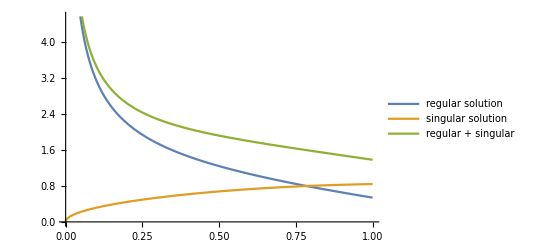

```mathematica
Plot[{sln3/.{ C[1]->1, C[2]->0},sln3/.{ C[1]->0, C[2]->1},sln3/.{ C[1]->1, C[2]->1}},{x,0,1},]
```

## Exercise 4

Identify the regular and singular components of the series solution centered at x_o=0 for the following differential equation:

x y''(x)+2y'(x)+y(x)=0

### Solution

The series solution can be obtained using AsymptoticDSolveValue:

```mathematica
sln4=AsymptoticDSolveValue[x y''[x]+2y'[x]+y[x]==0,y[x],{x,0,4}]
```

(1-x/2+x^2/12-x^3/144) C[2]+C[1] ((36+36 x-45 x^2+10 x^3)/(36 x)-1/12 (12-6 x+x^2) Log[x])

It can be seen that the series with the coefficient of C_1 has a term that is proportional to 1/x and log(x).

These terms are singular at x=0, so that is the singular component of the solution.

The series with the coefficient of c_2 is finite at x=0, so that is the regular component of the solution.

This can be observed from the plot of each series:

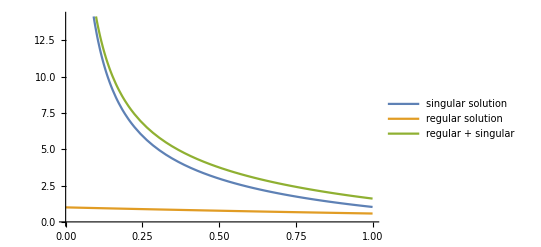

```mathematica
Plot[{sln4/.{ C[1]->1, C[2]->0},sln4/.{ C[1]->0, C[2]->1},sln4/.{ C[1]->1, C[2]->1}},{x,0,1},]
```

## Exercise 5

Identify the regular and singular components of the series solution centered at x_o=0 for the following differential equation:

x y''(x)+(1-x)y'(x)+y(x)=0

### Solution

The series solution can be obtained using AsymptoticDSolveValue:

```mathematica
sln5=AsymptoticDSolveValue[x y''[x]+(1-x)y'[x]+y[x]==0,y[x],{x,0,4}]
```

(1-x) C[1]+C[2] (3 x-x^2/4-x^3/36-x^4/288+(1-x) Log[x])

It can be seen that the second series has a term proportional to x log(x), which is singular at x=0, so that is the singular component of the solution.

Should this say “The first term of the series”?

The first term series, (1-x)C_1, is finite at x=0, so this is the regular component of the solution.

This can be observed from the plot of each series:

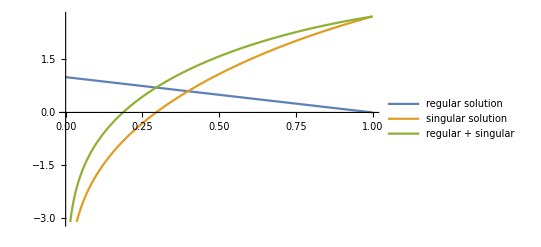

```mathematica
Plot[{sln5/.{ C[1]->1, C[2]->0},sln5/.{ C[1]->0, C[2]->1},sln5/.{ C[1]->1, C[2]->1}},{x,0,1},]
```

## Exercise 20—Special Functions

## Exercise 1

Find two solutions to the following differential equation:

x^2 y''(x)+x y'(x)+(x^2-9/4)y(x)=0

### Solution

This differential equation is in the form of a Bessel equation:

x^2 y''(x)+x y'(x)+(x^2-n^2)y(x)=0

Comparing the two equations, it can be seen that n=3/2.

Solve this equation using DSolveValue:

```mathematica
sln=DSolveValue[x^2 y''[x]+x y'[x]+(x^2-9/4)y[x]==0,y[x],x]
```

(√(2/π) C[2] (-Cos[x]/x-Sin[x]))/(√x)+(√(2/π) C[1] (-Cos[x]+Sin[x]/x))/(√x)

The solutions returned by DSolveValue can be identified as a linear combination of the two types of Bessel functions:

```mathematica
C[1]BesselJ[3/2,x]+C[2]BesselY[3/2,x]
```

(√(2/π) C[2] (-Cos[x]/x-Sin[x]))/(√x)+(√(2/π) C[1] (-Cos[x]+Sin[x]/x))/(√x)

While Bessel functions are indeed special functions, they can sometimes take elementary forms.

It turns out that for any integer n, the Bessel function of order n+1/2 is an elementary function.

## Exercise 2

Identify the following differential equation and find one solution based on the values of the parameters:

x(1-x) y''(x)+(1-x)y'(x)+y(x)=0

### Solution

This differential equation is in the form of a hypergeometric equation:

x(1-x)y''(x)+(c-(a+b+1)x)y'(x)-a b y(x)=0

Comparing the equations, you see that the parameters are a=1, b=-1, c=1.

Therefore, the one solution can be seen to be:

```mathematica
Hypergeometric2F1[1,-1,1,x]
```

1-x

Confirm that this is a solution by substituting it back into the differential equation:

```mathematica
(x(1-x)y''[x]+(1-x)y'[x]+y[x]==0)/.y->Function[x,Hypergeometric2F1[1,-1,1,x]]
```

True

## Exercise 3

Identify the following differential equation and find a solution to the initial value problem:

y''(x)-x y(x)=0

y(0)=1

y'(0)=1

### Solution

This differential equation is in the form of an Airy equation:

y''(x)-x y(x)=0

Therefore the general solution is a linear combination of two Airy functions:

```mathematica
genSol[x_]=DSolveValue[y''[x]-x y[x]==0,y[x],x]
```

AiryAi[x] C[1]+AiryBi[x] C[2]

Use the initial conditions to solve for the constants:

```mathematica
constants=Solve[{genSol[0]==1,genSol'[0]==1},{C[1],C[2]}][[1]]
```

{C[1]→1/2 (-3^(1/3) Gamma[1/3]+3^(2/3) Gamma[2/3]),C[2]→1/6 (3^(5/6) Gamma[1/3]+3 3^(1/6) Gamma[2/3])}

Use the values for the constants in the general solution to solve the initial value problem:

```mathematica
(genSol[x]/.constants)//Simplify
```

1/6 (3^(1/6) AiryBi[x] (3^(2/3) Gamma[1/3]+3 Gamma[2/3])+3 AiryAi[x] (-3^(1/3) Gamma[1/3]+3^(2/3) Gamma[2/3]))

Confirm the result by solving the initial value problem with DSolveValue:

```mathematica
DSolveValue[{y''[x]-x y[x]==0,y[0]==1,y'[0]==1},y[x],x]//Simplify
```

1/6 (3^(1/6) AiryBi[x] (3^(2/3) Gamma[1/3]+3 Gamma[2/3])+3 AiryAi[x] (-3^(1/3) Gamma[1/3]+3^(2/3) Gamma[2/3]))

## Exercise 4

Identify the following differential equation and find a solution to the initial value problem:

(1-x^2)y''(x)-2 x y'(x)+20y(x)=0

y(0)=0

y'(0)=-1

### Solution

This differential equation is in the form of a Legendre equation:

(1-x^2)y''(x)-2 x y'(x)+n(n+1)y(x)=0

Therefore, the general solution will be a linear combination of two Legendre functions:

```mathematica
genSol[x_,n_]=DSolveValue[(1-x^2)y''[x]-2 x y'[x]+n(n+1)y[x]==0,y[x],x]
```

C[1] LegendreP[n,x]+C[2] LegendreQ[n,x]

Comparing the general form of the Legendre equation and the equation in this exercise, it is seen that n=4.

Next, use the initial conditions to solve for the constants:

```mathematica
constants=Solve[{genSol[0,4]==0,(D[genSol[x,4],x]/.x->0)==-1},{C[1],C[2]}][[1]]
```

{C[1]→0,C[2]→-3/8}

Use the values for the constants in the general solution to solve the initial value problem:

```mathematica
(genSol[x,4]/.constants)//FullSimplify
```

1/64 (5 x (-11+21 x^2)-3 (3-30 x^2+35 x^4) ArcTanh[x])

Compare this result with DSolveValue:

```mathematica
DSolveValue[{(1-x^2)y''[x]-2 x y'[x]+20y[x]==0,y[0]==0,y'[0]==-1},y[x],x]//FullSimplify
```

1/64 (5 x (-11+21 x^2)-3 (3-30 x^2+35 x^4) ArcTanh[x])

## Exercise 5

Find the function that the hypergeometric function _2 F_1(a,b,a,x/a) converges to in the limit of b->∞.

### Solution

First, evaluate this Hypergeometric2F1 function in the Wolfram Language:

```mathematica
Hypergeometric2F1[a,b,a,x/b]
```

(1-x/b)^-b

Calculate the limit of this result as b->∞:

```mathematica
Limit[(1-x/b)^-b,b->Infinity]
```

ⅇ^x

It can be seen that in the limit this hypergeometric function converges to the exponential function.

This result can be calculated more directly in the following way:

```mathematica
Limit[Hypergeometric2F1[a,b,a,x/b],b->∞]
```

ⅇ^x